# Computerpraktikum

## Nützliche Funktionen und technisches

```mathematica
<<ErrorBarPlots`
```

```mathematica
Exportq[name_,data_]:=Export[DIR[StringJoin[name,".eps"]],data]

(* Ergebnisse darstellen *)
PlotResult[result_]:=PlotResult[result,{}]
PlotResult[result_,options_]:=Module[{
data,rangePlot,range,
startValx,endValx,addValx,
startValy,endValy,addValy
},
data=(dataset/.result);

(* Wenn es keine Eingangsfehler gibt, Fehler für Darstellung auf 0 setzen *)
If[Length[data[[1]]]==2,data=Replace[data,{Temp`x_,Temp`y_}-> {Temp`x,Temp`y,0},1]];

(* Automatisch den Zeichenbereich der Geraden bestimmen *)
startValx=Min[data[[All,1]]];
endValx=Max[data[[All,1]]];
addValx=Abs[startValx-endValx]*0.06;

startValy=Min[data[[All,2]]];
endValy=Max[data[[All,2]]];
addValy=Abs[startValy-endValy]*0.05;

range=PlotRange/.options;

rangePlot=If[range===PlotRange,{{startValx-addValx,endValx+addValx},{startValy-addValy,endValy+addValy}},range];
(* Plotten *)
Show[
Append[Append[ErrorListPlot[
data,
PlotRange-> rangePlot
],options],{PlotLabel->(NAME/.result)}]
,Plot[{
b t + a/.result,
}
,{t,startValx-addValx*50,endValx+addValx*50}
,PlotStyle-> {Automatic,Dashed,Dashed}
]
]
]

(* Warnung ausgeben *)
PrintWarning[text_]:=Print[Style[text,Bold,Orange]];

(* Wert ausgeben *)
PrintVal[name_,value_]:=(
Print[Row[{Style[name,Bold],": ",value}]];
)
PrintVal[value_]:=(
Print[Row[{Style[SymbolName[Unevaluated[value]],Bold],": ",value}]];
)
SetAttributes[PrintVal,HoldFirst]
```

```mathematica
ExpToLin[dataExp_]:=Replace[dataExp,{Temp`x_,Temp`y_,Temp`Δy_}-> {Temp`x,Log[Abs[Temp`y]],(Temp`Δy)/(Temp`y)},1]
ExpToLinOffset[dataExp_,offset_]:=Replace[dataExp,{Temp`x_,Temp`y_,Temp`Δy_}-> {Temp`x,Log[Abs[Temp`y]-offset],(Temp`Δy)/(Abs[Temp`y]-offset)},1]
ShowExpResult[s_]:=(
Print[Row[{NAME/.s,", exp Auswertung: A=",Exp[a/.s]//N," b=",b/.s}]];
)
List3to2[list_]:=Replace[list,{a_,b_,c_}->{a,b},1]
```

## Aufgabe 1

a. Erstellen der Funktion LinReg

```mathematica
LinReg[list_]:=
Module[
{ (* lokale Variablen *)
x,y,Δy,n,
S,ybar,datasetName,
a0,b0,Δa0,Δb0,
R2,χ2n
},

(* Name der Daten-Variable bestimmen *)
datasetName="";

(* Aufbereitung Daten *)
x=list[[All,1]];
y=list[[All,2]];
Δy=list[[All,3]];
n=Length[x];

(* Berechnung der Werte *)
S=∑_(i=1)^n 1/Δy[[i]]^2*∑_(i=1)^n x[[i]]^2/Δy[[i]]^2-(∑_(i=1)^n x[[i]]/Δy[[i]]^2)^2;
a0=1/S(∑_(i=1)^n x[[i]]^2/Δy[[i]]^2*∑_(i=1)^n y[[i]]/Δy[[i]]^2-∑_(i=1)^n x[[i]]/Δy[[i]]^2*∑_(i=1)^n (x[[i]]*y[[i]])/Δy[[i]]^2);
b0=1/S(∑_(i=1)^n 1/Δy[[i]]^2*∑_(i=1)^n (x[[i]]*y[[i]])/Δy[[i]]^2-∑_(i=1)^n x[[i]]/Δy[[i]]^2*∑_(i=1)^n y[[i]]/Δy[[i]]^2);
Δa0=√(1/S ∑_(i=1)^n x[[i]]^2/Δy[[i]]^2);
Δb0=√(1/S∑_(i=1)^n 1/Δy[[i]]^2);

(* Eigene Werte nach Aufgabe 1. *)
ybar=∑_(i=1)^n y[[i]]/Δy[[i]]^2/∑_(i=1)^n 1/Δy[[i]]^2;

R2=1-∑_(i=1)^n (y[[i]]-a0-b0 x[[i]])^2/Δy[[i]]^2/∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2;
χ2n=∑_(i=1)^n (1/Δy[[i]](y[[i]]-a0-b0 x[[i]]))^2 /(n-2);

(* Ausgabe der Ergebnisse *)
(*
CellPrint[TextCell[Row[{"Auswertung aus Eingangsfehlern ",Style[datasetName,Italic]}],"Subsection"]];*)

Print[TableForm[{{b0//N,Δb0//N},{a0//N,Δa0//N}},TableHeadings->{{"Steigung b","Achsenabschnitt a"},{"Wert","Fehler"}} ]];

Print[Row[{"Anzahl n: ",n,", R^2: ", R2//N,", χ^2/(n - 2): ",χ2n//N}]];
(*
(* Analyse-Informationen ausgeben *)
(*If[χ2n>1,"Warnung: Eingangfehler scheinen unplausibel, χ^2/(n-2) > 1"//PrintWarning];*)
*)
(* Ergebnisvariablen zurückgeben *)
{Symbol["b"]->b0,Symbol["Δb"]-> Δb0,Symbol["a"]-> a0,Symbol["Δa"]-> Δa0,Symbol["n"]-> n,Symbol["R2"]-> R2,Symbol["χ2n"]-> χ2n,
Symbol["NAME"]-> datasetName,Symbol["dataset"]-> (Evaluate[list])}
]
SetAttributes[LinReg,HoldFirst]
```

```mathematica
LinRegVar[list_]:=
Module[
{ (* lokale Variablen *)
x,y,n,
S,sQuadrat,datasetName,
a0,b0,Δa0,Δb0,R2
},

datasetName="";
(* Aufbereitung Daten *)
x=list[[All,1]];
y=list[[All,2]];
n=Length[x];
S=n∑_(i=1)^n x[[i]]^2-(∑_(i=1)^n x[[i]])^2;
a0=1/S(∑_(i=1)^n x[[i]]^2∑_(i=1)^n y[[i]]-∑_(i=1)^n x[[i]]∑_(i=1)^n (x[[i]]y[[i]]));
b0=1/S(n∑_(i=1)^n x[[i]]y[[i]]-∑_(i=1)^n x[[i]]∑_(i=1)^n y[[i]]);
sQuadrat=1/(n-2)∑_(i=1)^n (y[[i]]-a0-b0 x[[i]])^2;

Δa0=√(sQuadrat/S∑_(i=1)^n x[[i]]^2);
Δb0=√(n*sQuadrat/S);
R2=1-∑_(i=1)^n (y[[i]]-a0-b0 x[[i]])^2/∑_(i=1)^n (y[[i]]-1/n∑_(i=1)^n y[[i]])^2;

(* Ausgabe der Ergebnisse *)
(* CellPrint[TextCell[Row[{"Auswertung aus Varianz ",Style[datasetName,Italic]}],"Subsection"]];*)

Print[TableForm[{{b0//N,Δb0//N},{a0//N,Δa0//N}},TableHeadings->{{"Steigung b","Achsenabschnitt a"},{"Wert","Fehler"}} ]];
(*
Print[Row[{"Anzahl n: ",n,", R^2: ", R2}]];
*)

(* Ergebnisvariablen zurückgeben *)
{Symbol["b"]->b0,Symbol["Δb"]-> Δb0//N,Symbol["a"]-> a0//N,Symbol["Δa"]-> Δa0//N,Symbol["n"]-> n,Symbol["R2"]-> R2//N,
Symbol["NAME"]-> datasetName,Symbol["dataset"]-> (Evaluate[list])}
]
SetAttributes[LinRegVar,HoldFirst]
```

```mathematica
LinRegOrigin[list_]:=
Module[
{ (* lokale Variablen *)
x,y,Δy,n,
ybar,datasetName,
b0,Δb0,
R2,χ2n
},

(* Name der Daten-Variable bestimmen *)
datasetName="";

(* Aufbereitung Daten *)
x=list[[All,1]];
y=list[[All,2]];
Δy=list[[All,3]];
n=Length[x];

(* Berechnung der Werte *)
b0=∑_(i=1)^n (x[[i]]y[[i]])/Δy[[i]]^2/∑_(i=1)^n x[[i]]^2/Δy[[i]]^2;

Δb0=1/√(∑_(i=1)^n x[[i]]^2/Δy[[i]]^2);
χ2n=(∑_(i=1)^n ((y[[i]]-b0 x[[i]])/Δy[[i]])^2)/(n-1);
ybar=∑_(i=1)^n y[[i]]/Δy[[i]]^2/∑_(i=1)^n 1/Δy[[i]]^2;
R2=1-(∑_(i=1)^n (y[[i]]-b0 x[[i]])^2/Δy[[i]]^2)/(∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2);


(* Ausgabe der Ergebnisse *)

Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{b0//N,Δb0//N},{0,0}},TableHeadings->{{"Steigung b","Achsenabschnitt a"},{"Wert","Fehler"}} ]];

PrintVal["Anzahl Messdaten",n];
PrintVal["R^2", R2//N];
PrintVal["χ^2/(n - 1)",χ2n//N];

(* Analyse-Informationen ausgeben *)
If[χ2n>1,"Warnung: Eingangfehler scheinen unplausibel, χ^2/(n-2) > 1"//PrintWarning];

(* Ergebnisvariablen zurückgeben *)
{Symbol["b"]->b0//N,Symbol["Δb"]-> Δb0//N,Symbol["a"]-> 0,Symbol["Δa"]-> 0,Symbol["n"]-> n//N,Symbol["R2"]-> R2//N,Symbol["χ2n"]-> χ2n//N,
Symbol["NAME"]-> datasetName,Symbol["dataset"]-> (Evaluate[list])}
]
SetAttributes[LinRegOrigin,HoldFirst]



Eigentliche Auswertung
```

Auswertung Eigentliche

```mathematica
values={{1^2+1^2,59.9,1.5},{2^2,114.4,3.2},{2^2+1^2,134.2,4.1},{2^2+2^2,219.4,2.3},{3^2,246.3,2.9},{3^2+1,260.6,3.4}};
valueso3={{1^2+1^2,59.9,1.5},{2^2,114.4,3.2},{2^2+1^2,134.2,4.1},{2^2+2^2,219.4,2.3},{3^2,246.3,2.9}};
```

```mathematica
LinReg[valueso3];
LinReg[values];
```

| Wert | Fehler
Steigung b | 26.5772 | 0.364281
Achsenabschnitt a | 6.58955 | 1.96843

Anzahl n: 5, R^2: 0.999638, χ^2/(n - 2): 0.641776

| Wert | Fehler
Steigung b | 26.0659 | 0.31843
Achsenabschnitt a | 8.14699 | 1.8932

Anzahl n: 6, R^2: 0.998469, χ^2/(n - 2): 2.56869

```mathematica
Solve[26.57==12.26^2/(a^2*Sin[43*180/Pi]^2),a]
12.26/(Sqrt[26.577]*Sin[43*180/Pi])
12.26/(26.577^(3/2)*Sin[43*180/Pi]*2) *0.364
```

{{a→-3.64938},{a→3.64938}}

3.6489

0.0249878

| Wert | Fehler
Steigung b | 26.5772 | 0.364281
Achsenabschnitt a | 6.58955 | 1.96843

Anzahl n: 5, R^2: 0.999638, χ^2/(n - 2): 0.641776

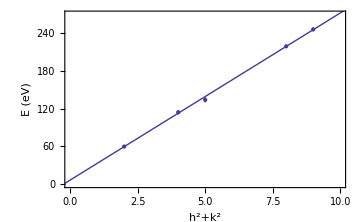

```mathematica
Show[PlotResult[LinReg[valueso3],PlotRange->{{0,10},{0,270}}],ImageSize->Medium, AspectRatio->GoldenRatio^-1,Frame->True,Axes->{True,False},AxesOrigin->{0,0},
FrameLabel->{"h^2+k^2","E (eV)"}]
```

```mathematica
<<PhysicalConstants`

IV Kurve
```

IV Kurve

| Wert | Fehler
Steigung b | 19.2231 | 0.0262817
Achsenabschnitt a | 93.1565 | 0.19936

Anzahl n: 5, R^2: 0.993848, χ^2/(n - 2): 1103.82

| Wert | Fehler
Steigung b | 14.3085 | 0.019509
Achsenabschnitt a | 42.1984 | 0.257592

Anzahl n: 5, R^2: 0.999301, χ^2/(n - 2): 125.481

| Wert | Fehler
Steigung b | 11.3655 | 0.0154915
Achsenabschnitt a | -10.2267 | 0.322319

Anzahl n: 5, R^2: 0.999921, χ^2/(n - 2): 14.1933

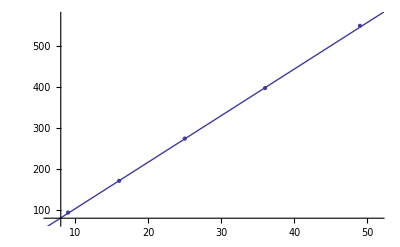

| Wert | Fehler
Steigung b | 11.4047 | 0.058737
Achsenabschnitt a | -10.3579 | 1.79297

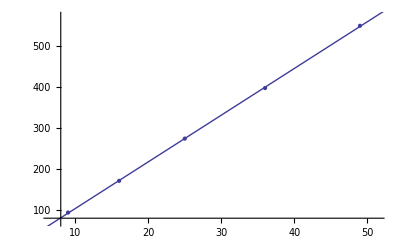

| Wert | Fehler
Steigung b | 9.41666 | 0.0128393
Achsenabschnitt a | -63.3316 | 0.390442

Anzahl n: 5, R^2: 0.999278, χ^2/(n - 2): 129.638

```mathematica
iv1={{1,93.78,0.43},{2^2,171.31,0.15},{3^2,274.55,0.31},{4^2,398.04,0.39},{5^2,550.16,0.97}};
iv2={{4,93.78,0.43},{3^2,171.31,0.15},{4^2,274.55,0.31},{5^2,398.04,0.39},{6^2,550.16,0.97}};
iv3={{3^2,93.78,0.43},{4^2,171.31,0.15},{5^2,274.55,0.31},{6^2,398.04,0.39},{7^2,550.16,0.97}};
iv4={{4^2,93.78,0.43},{5^2,171.31,0.15},{6^2,274.55,0.31},{7^2,398.04,0.39},{8^2,550.16,0.97}};
PlotResult[LinReg[iv1]];
PlotResult[LinReg[iv2]];
PlotResult[LinReg[iv3]]
PlotResult[LinRegVar[iv3]]
PlotResult[LinReg[iv4]];
```

```mathematica
Convert[1/Sqrt[Convert[11.4047ElectronVolt,Joule]*8*ElectronMass/PlanckConstant^2],Angstrom]*1/Sin[92*Pi/180]*2
x=11.4047 ElectronVolt;
dx=0.058737ElectronVolt;
z=94*Pi/180;
dz=1*Pi/180;
Sqrt[Convert[(PlanckConstant/(Sqrt[8 ElectronMass]*2*Sin[z])*x^(-3/2)*dx)^2,Angstrom^2]+Convert[(PlanckConstant/(Sqrt[8 ElectronMass*x]*Sin[z]^2)*Cos[z]*dz)^2,Angstrom^2]]*2
iv3//TableForm
```

3.63383 Angstrom

0.0103743 √(Angstrom^2)

9 | 93.78 | 0.43
16 | 171.31 | 0.15
25 | 274.55 | 0.31
36 | 398.04 | 0.39
49 | 550.16 | 0.97

| Wert | Fehler
Steigung b | 11.3655 | 0.0154915
Achsenabschnitt a | -10.2267 | 0.322319

Anzahl n: 5, R^2: 0.999921, χ^2/(n - 2): 14.1933

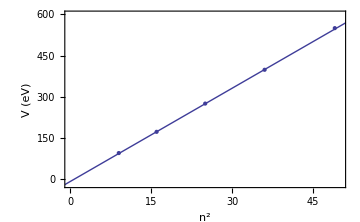

| Wert | Fehler
Steigung b | 11.4047 | 0.058737
Achsenabschnitt a | -10.3579 | 1.79297

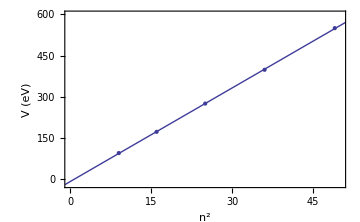

```mathematica
Show[PlotResult[LinReg[iv3],PlotRange->{{0,50},{-20,600}}],ImageSize->Medium, AspectRatio->GoldenRatio^-1,Frame->True,Axes->{True,False},AxesOrigin->{0,0},
FrameLabel->{"n^2","V (eV)"}]
Show[PlotResult[LinRegVar[iv3],PlotRange->{{0,50},{-20,600}}],ImageSize->Medium, AspectRatio->GoldenRatio^-1,Frame->True,Axes->{True,False},AxesOrigin->{0,0},
FrameLabel->{"n^2","V (eV)"}]
```